```mathematica
Clear["Global`*"];
ClearSystemCache[];
SetDirectory[NotebookDirectory[]];
```

```mathematica
Install["Suave-Linux"];
```

## Constants

```mathematica
Clear[mn];
mn=QuantityMagnitude[Quantity["NeutronMass"], "Gigaelectronvolts"/"SpeedOfLight"^2];
G =  6.67408*^-11; (*Grav Constant*)
hbarc = QuantityMagnitude[Quantity["ReducedPlanckConstant"]*Quantity["SpeedOfLight"], "Gigaelectronvolts"*"Femtometers" ]; (* in GeV fm *)
vs=230*^3;
vd=270*^3;
cspeed=QuantityMagnitude[Quantity["SpeedOfLight"], "Meters"/"Seconds"];
km=1000;
cm=1/100;
Gevto1fm=1000/197.3;
fm1to1m=10^15;
ρχ=0.4*^6; 
Prefactor=1;(*1/6.58*^-25; *)(* for d0 *)
ϵreg=10^(-4);
v=246;
cns=1;(*needs to be fixed*)
```

## Neutron Star EoS

#### Load in data

```mathematica
EoSHeaders = Import["eos_24_lowmass.dat"];
Dataset[EoSHeaders[[1,All]]] (*Print out headings so I know what I'm doing *)
EoSData =Drop[EoSHeaders, 1] ;(* Remove Headings *)
```

Dataset[<>]

Make Interpolating Functions

```mathematica
radius = EoSData[[All,1]];

rMin = radius[[1]];
rMax = Rstar= 11.;

μf[x_]:= Interpolation[ EoSData[[All, {1,8}]] ][x*Rstar]*1*^-3; (* Chemical potential in GeV *)

nb          = EoSData[[All,3]];
Yn          = EoSData[[All, 7]];
muList = EoSData[[All, 8]];

ndList = nb*Yn;
nprof=Interpolation[ Transpose[{radius,nb*Yn}]]; (* Neutron density in fm^-3*)

MNS = Interpolation[EoSData[[All, {1, 2}]]]; (* In units of M_⊙ *) 

p =Interpolation[EoSData[[All, {1, 12}]]]; (* in dyn/cm^2*)
```

```mathematica
EscVelSetUp[rad_?NumericQ] := Module[                                                           (* escape velocity inside star, in natural units *)
{GravPot,r}, 
GravPot =NIntegrate[(2.*G*MNS[r]*2.*^30)/(r^2*1.*^3), {r, rad, rMax}];
Sqrt[GravPot +(2.*G*MNS[rMax]*2.*^30)/(rMax*1.*^3)]/cspeed
]; 


ve = Interpolation[Table[{ri, EscVelSetUp[ri]}, {ri, rMin, Last[radius]}]];
```

```mathematica
(*Define Rstar, ζ0, B[r], nprof[r] (the true baryon density, NOT energy density) and μf[r].
Rstar in kmeters
nprof in the unit you want, I use fm^-3
ζ0 in the right unit to match nprof and nfree (That is in GeV^3)
μf in GeV
 IMPORTANT: definitions have to be functions that can be evaluated fast!*)
```

```mathematica
rtA[r_]:=Sqrt[1/(1 -(2*G*MNS[r*Rstar]*2*^30)/(r*Rstar*1*^3*cspeed^2))];
```

```mathematica
Clear[B];
B =NDSolveValue[{y'[x]==(2*G*(Rstar*1*^3))/(cspeed^2*(x*(Rstar*1*^3))^2)*((MNS[x*Rstar]*2*^30+p[x*Rstar]*0.1*(x*(Rstar*1*^3))^3/cspeed^2)/( 1 - (2*G*MNS[x*Rstar]*2*^30)/(cspeed^2*(x*(Rstar*1*^3)))))*y[x], y[1]==(1 - (2*G*MNS[1*Rstar]*2*^30)/(cspeed^2*(Rstar*1*^3)))},y, {x, rMin/Rstar, 1}];
(*takes as input r/Rstar (from 0 to 1)*)
```

```mathematica
ζ0=5.278368626202642(*Note that is not a problem that it is >1, as I use different units for ntrue and nfree, in same units result is 0.04*);
```

## Cross sections

```mathematica
μ[mχ_] := mχ/mn;
```

```mathematica
σ1[s_,t_,mχ_,Λ_]:=cns*mn^4(4mχ^2-t)(4mχ^2-mχ^2*t/mn^2)/(32Pi*mχ^2*β[s,mχ])/Λ^4;
```

```mathematica
(*Note: Λ is set to 1 when integrating, as result scales with 4rth inverse power*)
```

```mathematica
d0[s_,t_,mχ_,Λ_]:= 0.5*10^-19/(hbarc)^2; (* in GeV^-2 *)
d1[s_,t_,mχ_,Λ_]:= (mn^2*(4*mχ^2-t)*(4*mχ^2-μ[mχ]^2*t))/(32*π*μ[mχ]^2*s);
d2[s_,t_,mχ_,Λ_]:= (mn^2*t*(μ[mχ]^2*t - 4*mχ^2))/(32*π*s);
d3[s_,t_,mχ_,Λ_]:= (mn^2*t*(t - 4*mχ^2))/(32*π*s);
d4[s_,t_,mχ_,Λ_]:= (mn^2*t^2)/(32*π*s);
d5[s_,t_,mχ_,Λ_]:= (2*(μ[mχ]^2+1)^2*mχ^4-4*(μ[mχ]^2+1)*μ[mχ]^2*s*mχ^2+μ[mχ]^4*(2*s^2+2*s*t+t^2))/(16*π*μ[mχ]^4*s);
d6[s_,t_,mχ_,Λ_]:= 1/(16*π*μ[mχ]^4*s)(2*(μ[mχ]^2-1)^2*mχ^4-4*(μ[mχ]^2*s +s+μ[mχ]^2*t)*μ[mχ]^2*mχ^2+μ[mχ]^4*(2*s^2+2*s*t+t^2));
d7[s_,t_,mχ_,Λ_]:= 1/(16*π*μ[mχ]^4*s)(2*(μ[mχ]^2-1)^2*mχ^4-4*(μ[mχ]^2*s +s+t)*μ[mχ]^2*mχ^2+μ[mχ]^4*(2*s^2+2*s*t+t^2));
d8[s_,t_,mχ_,Λ_]:= 1/(4*π*μ[mχ]^4*s)(2*(μ[mχ]^4+10*μ[mχ]^2+1)*mχ^4-4*(μ[mχ]^2+1)*μ[mχ]^2*mχ^2*(s+t)+μ[mχ]^4*(2*s^2+2*s*t+t^2));
d9[s_,t_,mχ_,Λ_]:= 1/(4*π*μ[mχ]^4*s)(4*(μ[mχ]^4+4*μ[mχ]^2+1)*mχ^4 - 2*(μ[mχ]^2+1)*μ[mχ]^2*mχ^2*(4*s+t)+μ[mχ]^4*(2*s+t)^2);
d10[s_,t_,mχ_,Λ_]:=1/(4*π*μ[mχ]^4*s)(4*(μ[mχ]^2-1)^2*mχ^4 - 2*(μ[mχ]^2+1)*μ[mχ]^2*mχ^2*(4*s+t)+μ[mχ]^4*(2*s+t)^2);
```

## Functions

```mathematica
(* Eu = E*mn*)
```

```mathematica
β[s_,mχ_]:=s-mn^2-mχ^2;
γ[s_,mχ_]:=Sqrt[β[s,mχ]^2-4mn^2*mχ^2];
Solutions[E1_,E2_,s_,t_,mχ_]:={(E2 mn^4 t-E2 mχ^4 t-2 E2 mn^2 s t+E2 s^2 t+2 E1^2 E2 (mn^4+(mχ^2-s) (mχ^2-s-t)+mn^2 (-2 mχ^2-2 s+t))+√((2 E1 E2+mn^2+mχ^2-s)^2 (4 E1^2 mn^2+mn^4+4 E2^2 mχ^2+mχ^4+4 E1 E2 (mn^2+mχ^2-s)-2 mχ^2 s+s^2-2 mn^2 (mχ^2+s)) t (mn^4+mχ^4-2 mχ^2 s-2 mn^2 (mχ^2+s)+s (s+t)))+E1 (mn^6+mχ^6+mn^4 (-mχ^2-3 s+t)-mχ^4 (3 s+t)-mn^2 (mχ^4+2 mχ^2 s-3 s^2-2 E2^2 t)-s (s^2+2 E2^2 t+s t)+mχ^2 (3 s^2-2 E2^2 t+2 s t)))/((2 E1 E2+mn^2+mχ^2-s) (mn^4+(mχ^2-s)^2-2 mn^2 (mχ^2+s))),(E2 mn^4 t-E2 mχ^4 t-2 E2 mn^2 s t+E2 s^2 t+2 E1^2 E2 (mn^4+(mχ^2-s) (mχ^2-s-t)+mn^2 (-2 mχ^2-2 s+t))-√((2 E1 E2+mn^2+mχ^2-s)^2 (4 E1^2 mn^2+mn^4+4 E2^2 mχ^2+mχ^4+4 E1 E2 (mn^2+mχ^2-s)-2 mχ^2 s+s^2-2 mn^2 (mχ^2+s)) t (mn^4+mχ^4-2 mχ^2 s-2 mn^2 (mχ^2+s)+s (s+t)))+E1 (mn^6+mχ^6+mn^4 (-mχ^2-3 s+t)-mχ^4 (3 s+t)-mn^2 (mχ^4+2 mχ^2 s-3 s^2-2 E2^2 t)-s (s^2+2 E2^2 t+s t)+mχ^2 (3 s^2-2 E2^2 t+2 s t)))/((2 E1 E2+mn^2+mχ^2-s) (mn^4+(mχ^2-s)^2-2 mn^2 (mχ^2+s)))};
EF[Eu_,s_,t_,mχ_,B_,μf_]:=If[s>mn^2+(2 Eu mn mχ)/(√B)+mχ^2,(E2+E1-Solutions[E1,E2,s,t,mχ][[1]]-mn-μf/.E1->mχ/Sqrt[B]/.E2->mn*Eu),(E2+E1-Solutions[E1,E2,s,t,mχ][[2]]-mn-μf/.E1->mχ/Sqrt[B]/.E2->mn*Eu)];
tmin[s_,mχ_]:=-γ[s,mχ]^2/s;
tmax=0;
smin[Eu_,mχ_,B_]:=mn^2+(2 Eu mn mχ)/(√B)-2 √(-1+1/B) √(-1+Eu^2) mn mχ+mχ^2;
smax[Eu_,mχ_,B_]:=mn^2+(2 Eu mn mχ)/(√B)+2 √(-1+1/B) √(-1+Eu^2) mn mχ+mχ^2;
Eumax[μf_,B_]:=Min[1+μf/mn,1/Sqrt[B]];
Eumin[mχ_,μf_,B_]:=Max[1,1+(Eumax[μf,B]-1)(1-mχ/mn)];

dσ[s_,t_,mχ_,Λ_]:=d1[s,t,mχ,Λ];

Integrand[r_,Eu_,s_,t_,mχ_]:=r^2*ζ[r]/B[r]^(1/2)dσ[s,t,mχ,1]*Eu*s/β[s,mχ]/γ[s,mχ]*HeavisideTheta[EF[Eu,s,t,mχ,B[r],μf[r]]];
IntegrandNoPauli[r_,Eu_,s_,t_,mχ_]:=r^2*ζ[r]/B[r]^(1/2)dσ[s,t,mχ,{1}]Eu*s/β[s,mχ]/γ[s,mχ];
Coeff[mχ_]:=2ρχ*Erf[Sqrt[3/2]vs/vd]*mn^2*(Rstar*1000)^3/(Pi*(vs/cspeed)*mχ^2);
nfree[r_]:=(2mn*μf[r])^(3/2)/(3Pi^2); (* in GeV^3 *)
ζ[r_]:= (*(nprof[r*Rstar]*rtA[r])/(nprof[rMin]*rtA[rMin/Rstar])*ζ0*nfree[rMin/Rstar]/nfree[r];*)(nprof[r*Rstar]*hbarc^3)/(nfree[r]*rtA[r]);
```

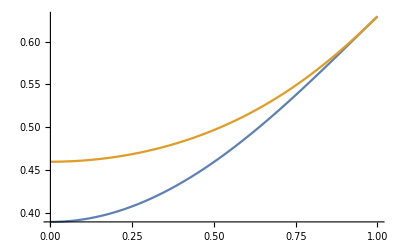

```mathematica
Plot[{1 - ve[x*Rstar]^2, B[x]}, {x, rMin/Rstar, 1}]
```

## Integrating

### Definitions

```mathematica
CrateT[mχ_]:=Prefactor*Coeff[mχ]*NIntegrate[Integrand[r,Eu,s,t,mχ],{r,0,1-ϵreg},{Eu,Eumin[mχ,μf[r],B[r]],Eumax[μf[r],B[r]]},{s,smin[Eu,mχ,B[r]],smax[Eu,mχ,B[r]]},{t,tmin[s,mχ],tmax},Method->"Trapezoidal",PrecisionGoal->5,AccuracyGoal->4,WorkingPrecision->15];
CrateM[mχ_]:=Prefactor*Coeff[mχ]*NIntegrate[Integrand[r,Eu,s,t,mχ],{r,0,1-ϵreg},{Eu,Eumin[mχ,μf[r],B[r]],Eumax[μf[r],B[r]]},{s,smin[Eu,mχ,B[r]],smax[Eu,mχ,B[r]]},{t,tmin[s,mχ],tmax},Method->"MonteCarlo",PrecisionGoal->5,AccuracyGoal->4,WorkingPrecision->15];
(*===========================================================*)

CrateQM[mχ_]:=Prefactor*Coeff[mχ]*NIntegrate[Integrand[r,Eu,s,t,mχ],{r,rMin/Rstar,1-ϵreg},{Eu,Eumin[mχ,μf[r],B[r]],Eumax[μf[r],B[r]]},{s,smin[Eu,mχ,B[r]],smax[Eu,mχ,B[r]]},{t,tmin[s,mχ],tmax},Method->"QuasiMonteCarlo",PrecisionGoal->5,AccuracyGoal->4,WorkingPrecision->15];
(*===========================================================*)

CrateSuave[mχ_]:=Prefactor*Coeff[mχ]*Part[Suave[Integrand[r,Eu,s,t,mχ],{r,rMin/Rstar,1-ϵreg},{Eu,Eumin[mχ,μf[r],B[r] ],Eumax[μf[r],B[r]] },{s,smin[Eu,mχ,B[r]] ,smax[Eu,mχ,B[r]] },{t,tmin[s,mχ],tmax},PrecisionGoal->5,AccuracyGoal->4, Verbose->0],1,1];
(*===========================================================*)
```

```mathematica
CrateTNoPauli[mχ_]:=Coeff[mχ]*NIntegrate[IntegrandNoPauli[r,Eu,s,t,mχ],{r,rMin/Rstar,1-ϵreg},{Eu,Eumin[mχ,μf[r],B[r]],Eumax[μf[r],B[r]]},{s,smin[Eu,mχ,B[r]],smax[Eu,mχ,B[r]]},{t,tmin[s,mχ],tmax},Method->"Trapezoidal",PrecisionGoal->5,AccuracyGoal->4,WorkingPrecision->15];
```

### Results (No Pauli Blocking)

```mathematica
(*ParallelTable[{10^lm,Crate[10^lm]},{lm,-3,3}](*No Pauli blocking*)*)
```

```mathematica
Correct behaviour: 1/m for m<<mn, constant for m>>mn, as cross section is proportional to mχ
```

### Integration Strategies: No Pauli blocking

```mathematica
(*Crate[1000]//Timing(*Globaladaptive*)*)
```

```mathematica
(*Crate[1000]//Timing(*localadaptive: too long*)*)
```

```mathematica
(*Crate[1000]//Timing(*trapezoidal*)*)
```

```mathematica
(*Crate[1000]//Timing(*montecarlo*)*)
```

```mathematica
(*Crate[1000]//Timing(*quasimontecarlo*)*)
```

```mathematica
(*Crate[1000]//Timing(*adaptivemontecarlo*)*)
```

```mathematica
(*Crate[1000]//Timing(*adaptivequasimontecarlo*)*)
```

### Integration Strategies: Pauli blocking

#### mχ=1TeV

```mathematica
(*Crate[1000]//Timing(*Globaladaptive: too long*)*)
```

```mathematica
(*Crate[1000]//Timing(*trapezoidal*)*)
```

```mathematica
(*Crate[1000]//Timing(*montecarlo*)*)
```

```mathematica
(*Crate[1000]//Timing(*quasimontecarlo*)*)
```

#### mχ=1GeV

```mathematica
(*CrateT[1]//Timing(*trapezoidal*)*)
```

```mathematica
(*CrateM[1]//Timing(*montecarlo*)*)
```

```mathematica
(*CrateQM[1]//Timing(*quasimontecarlo*)*)
```

```mathematica
(*CrateSuave[1]//Timing*)
```

#### mχ=1MeV

```mathematica
(*CrateT[0.001]//Timing(*trapezoidal*)*)
```

```mathematica
(*CrateM[0.001]//Timing(*montecarlo*)*)
```

```mathematica
(*CrateQM[0.001]//Timing(*quasimontecarlo*)*)
```

```mathematica
(*Montecarlo and QuasiMontecarlo fail below 1 GeV*)
```

```mathematica
(*CrateSuave[0.001]//Timing*)
```

## Plots

```mathematica
(*capOutS1 = With[{x:=10^xp}, Table[{x, CrateSuave[d0,x]}, {xp, -4.6, -1.3, 0.2}]];*)
```

```mathematica
(*capOutQM = With[{x:=10^xp}, Table[{x, CrateQM[d0,x]}, {xp, -1.3, 1, 0.2}]];*)
```

```mathematica
(*capOutS2 = With[{x:=10^xp}, Table[{x, CrateSuave[d0,x]}, {xp, 1, 5, 0.2}]];*)
```

```mathematica
(*captot = Join[capOutS1, capOutQM, capOutS2];
Export["cap_test.dat", captot, "Table"]*)
```

## Export to .dat

```mathematica
Do[
Clear[capOut1, capOut2, capOut3, captot];
dσ[s_,t_,mχ_,Λ_]:=CS[s,t,mχ,Λ];
capOut1 = With[{x:=10^xp}, Table[{xp, CrateSuave[x]}, {xp, -4.8, -1, 0.2}]];
capOut2 = With[{x:=10^xp}, Table[{xp, CrateQM[x]}, {xp, -1, 2, 0.2}]];
capOut3 = With[{x:=10^xp}, Table[{xp, CrateSuave[x]}, {xp, 2, 5, 0.2}]];

captot = Join[capOut1, capOut2, capOut3];
Export[StringJoin[ToString[CS], "_cap.dat"], captot, "Table"]

,
{CS, {d0}}
]
```

Suave::success: Needed 1000 function evaluations on 1 subregions.

General::stop: Further output of Suave::success will be suppressed during this calculation.

```mathematica
(*capOut1 = With[{x:=10^xp}, Table[{x, CrateSuave[x]}, {xp, -4.6, -1.3, 0.2}]];
capOut2 = With[{x:=10^xp}, Table[{x, CrateQM[x]}, {xp, -1.3, 1, 0.2}]];
*)
```

```mathematica
(*capOut3 = With[{x:=10^xp}, Table[{x, CrateSuave[x]}, {xp, 1, 5, 0.2}]];*)
```

```mathematica
(*captot = Join[capOut1, capOut2, capOut3];
Export[StringJoin[ "d1_cap.dat"], captot, "Table"]*)
```